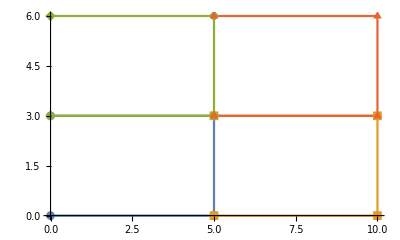

```mathematica
CreateRectangularMesh[a_,b_,nx_,ny_]:=Block[{cols,rows,coords,i,j,deltax,deltay,co1,co2,co3,co4,elvec},

cols=(nx+2);
rows=(ny+2);
coords=Table[0,{rows},{cols}];

deltax=(b[[1]]-a[[1]])/(nx+1);
deltay=(b[[2]]-a[[2]])/(ny+1);
xstart=a[[1]];
ystart=a[[2]];
temp={0,0};

For[i=1,i≤ rows,i++,
For[j=1,j≤cols,j++,
coords[[i,j]]={xstart,ystart};
xstart+=deltax;
];
ystart+=deltay;
xstart=a[[1]];
];

elvec={};
idvec={};
id=1;
For[i=1,i<rows,i++,
For[j=1,j<cols,j++,
co1=coords[[i,j]];
co2=coords[[i,j+1]];
co3=coords[[i+1,j]];
co4=coords[[i+1,j+1]];
AppendTo[elvec,{co1,co2,co4,co3}];
If[i==1,
AppendTo[idvec,{1,2,id+4ny,id+4nx+1}];
,

var=idvec[[i-1]]+{1,1,-1,-1};
AppendTo[idvec,var];
];

];
];
elvec
]
s=CreateRectangularMesh[{0,0},{10,6},1,1];
ListLinePlot[s,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
```

```mathematica
idvec
```

{{1,2,5,6},{1,2,5,6},{2,3,4,5},{2,3,4,5}}

```mathematica
allnodes=Flatten[s,1]
alreadcomputednodes={};
For[i=1,i≤Length[allnodes],i++,
node=allnodes[[i]];
For[j=1+i,j<Length[allnodes],j++,
If[node==allnodes[[j]], AppendTo[alreadcomputednodes,node]];
];
];
newnode=allnodes;
For[i=1,i<=Length[alreadcomputednodes],i++,
newnode=DeleteCases[newnode,alreadcomputednodes[[i]]];
AppendTo[newnode,alreadcomputednodes[[i]]];


];
Length[newnode]
```

{{0,0},{5,0},{5,3},{0,3},{5,0},{10,0},{10,3},{5,3},{0,3},{5,3},{5,6},{0,6},{5,3},{10,3},{10,6},{5,6}}

10

```mathematica
newnode
```

{{0,0},{10,0},{5,6},{0,6},{10,6},{5,6},{5,0},{0,3},{10,3},{5,3}}

```mathematica
MatchQ
```

```mathematica
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
GeneratePsis[order_]:=Block[{sz,i,j,w,psis,temp,xi,eta},
sz=(2+order-1)(2+order-1);
psis=Table[0,{sz}];
temp=1;
For[i=1,i≤ 1+order,i++,
For[j=1,j≤ 1+order,j++,
psis[[temp]]=(ComputeShape[order,xi][[j]]ComputeShape[order,eta][[i]])*(-1);
temp++;
];
];
psis
];
```

```mathematica
(*Plot3D[GeneratePsis[2],{xi,-1,1},{eta,-1,1}]*)
```

```mathematica
GeneratePsis[1]//Simplify
```

{-1/4 (-1+eta) (-1+xi),1/4 (-1+eta) (1+xi),1/4 (1+eta) (-1+xi),-1/4 (1+eta) (1+xi)}

```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order+1,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
Integrate[-GeneratePsis[1][[4]],{xi,-1.,1},{eta,-1,1}]
soma=0;
intrule=IntegrationRule[1];
For[i=1,i≤ Length[intrule],i++,
For[j=1,j≤ Length[intrule],j++,
soma+=(-GeneratePsis[1][[4]]/.{xi->intrule[[i,j,1]],eta->intrule[[i,j,2]]})intrule[[i,j,3]];
];
];
soma
```

1.

1.

```mathematica
intrule//MatrixForm
```

((-0.774597
0.774597
0.308642) | (0.
0.774597
0.493827) | (0.774597
0.774597
0.308642)
(-0.774597
0.
0.493827) | (0.
0.
0.790123) | (0.774597
0.
0.493827)
(-0.774597
-0.774597
0.308642) | (0.
-0.774597
0.493827) | (0.774597
-0.774597
0.308642))

```mathematica
intrule[[1,3]]
```

{0.774597,0.774597,0.308642}

```mathematica
GeneratePsis[1]
```

{-(1+1/2 (-1-eta)) (1+1/2 (-1-xi)),-1/2 (1+1/2 (-1-eta)) (1+xi),-1/2 (1+eta) (1+1/2 (-1-xi)),-1/4 (1+eta) (1+xi)}

```mathematica
Plot3D[GeneratePsis[1],{eta,-1,1},{xi,-1,1}]
```

-Graphics3D-

```mathematica
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta},
psis=GeneratePsis[order];
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]-1}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]-1}];
Jac={{D[x,xi],D[x,eta]},{D[y,xi],D[y,eta]}};
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
nodes[order_,coords_]:=Block[{matnode,w,xa,xb,newcoords,i,line1,line2,line3,line4,ya,yb,newtopol,x,y,nodes={},n,j,temp},
If[order==1,Return[coords]];
n=1;
xa=coords[[1,1]];
xb=coords[[2,1]];
y=coords[[1,2]];
line1=Table[{xa+(1-i)(xa-xb)/order,y},{i,1,order+n}];
ya=coords[[2,2]];
yb=coords[[3,2]];
x=coords[[2,1]];
line2=Table[{x,ya+(1-i)(ya-yb)/order},{i,1,order+n}];
xa=coords[[4,1]];
xb=coords[[3,1]];
y=coords[[3,2]];
line3=Table[{xa+(1-i)(xa-xb)/order,y},{i,1,order+n}];
ya=coords[[4,2]];
yb=coords[[1,2]];
x=coords[[1,1]];
line4=Table[{x,ya+(1-i)(ya-yb)/order},{i,1,order+n}];
(*Print[{line1,line2,line3,line4}];*)
Table[AppendTo[nodes,line1[[i]]],{i,1,Length[line1]}];
(*Print["1 = ",nodes];*)
Table[AppendTo[nodes,line2[[i]]],{i,1,Length[line2]}];
(*Print["2 = ",nodes];*)
Table[AppendTo[nodes,line3[[i]]],{i,1,Length[line3]}];
(*Print[ "3 = ",nodes];*)
Table[AppendTo[nodes,line4[[i]]],{i,1,Length[line4]}];
(*Print["4 = ",nodes];*)
For[i=1,i≤ Length[nodes],i++,
temp=nodes[[i]];
For[j=i+1,j≤ Length[nodes],j++,
If[temp==nodes[[j]],
nodes=Delete[nodes,j];

];
];
];
(*{line1,line2,line3,line4}*)
nodes
]
```

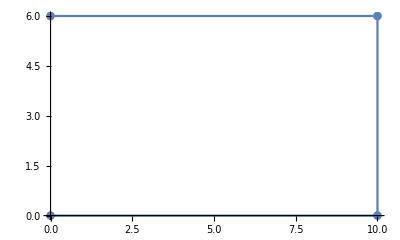

```mathematica
s=CreateRectangularMesh[{0,0},{10,6},0,0];
ListLinePlot[s,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True,PlotRange->All]
```

5

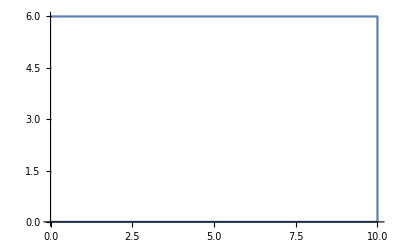

```mathematica
nels=Length[s];
p=1;
matnode=Table[0,{nels}];
nnodes=0;
4 nels p+1
For[i=1,i≤nels,i++,
matnode[[i]]=nodes[p,s[[i]]];
nnodes+=Length[matnode[[i]]];
];
ListLinePlot[matnode]
```

```mathematica
matnode
```

{{{0,0},{10,0},{10,6},{0,6}}}

```mathematica
nels
```

1

```mathematica
s[[1]]
```

{{0,0},{10,0},{10,6},{0,6}}

```mathematica
ID=1;
ndiv=1;
top=Table[0,{4^ndiv},{4}];
posi=1;
For[i=1,i≤ ndiv 2,i++,
Print["ID = ",ID];
For[j=ID,j<ID+ndiv 2,j++,
top[[posi]]={j,j+1,(j+1)+2ndiv,(j+1)+2ndiv+1};
posi++;
];
ID=(j+ndiv);
];
top
```

ID = 1

ID = 4

{{1,2,4,5},{2,3,5,6},{4,5,7,8},{5,6,8,9}}

```mathematica
ComputeNodeVec[matnode_]:=Block[{nnood,k,i},
nnood=Flatten[matnode,1];
nnood=SortBy[nnood, Last];
For[k=1,k<1000,k++,
For[i=1,i<Length[nnood],i++,
If[nnood[[i]]==nnood[[i+1]],nnood=Delete[nnood,i]];
];
];
nnood
];
ComputeNodeVec[matnode]
```

{{0,0},{10,0},{0,6},{10,6}}

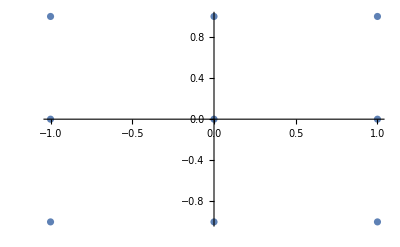

```mathematica
coordss={{-1,-1},{0,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{0,1},{1,1}};
topol={{1,2,4,5},{2,3,5,6},{4,5,7,8},{5,6,8,9}};
ListPlot[coordss]
```

```mathematica
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
GeneratePsis[order_]:=Block[{sz,i,j,w,psis,temp,xi,eta},
sz=(2+order-1)(2+order-1);
psis=Table[0,{sz}];
temp=1;
For[i=1,i≤ 1+order,i++,
For[j=1,j≤ 1+order,j++,
psis[[temp]]=(ComputeShape[order,xi][[j]]ComputeShape[order,eta][[i]])*(1);
temp++;
];
];
psis
];
```

```mathematica
psis1=GeneratePsis[1]
```

{(1+1/2 (-1-eta)) (1+1/2 (-1-xi)),1/2 (1+1/2 (-1-eta)) (1+xi),1/2 (1+eta) (1+1/2 (-1-xi)),1/4 (1+eta) (1+xi)}

```mathematica
psis2={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)}
```

{0.25 (1-eta) (1-xi),0.25 (1-eta) (1+xi),0.25 (1+eta) (1+xi),0.25 (1+eta) (1-xi)}

```mathematica
Simplify[psis1-psis2]
```

{0.,0.,0.+(-0.5-0.5 eta) xi,0.+(0.5+0.5 eta) xi}

```mathematica
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta},
(*psis=GeneratePsis[order];*)
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
(*Print["J12 = ",Jac[[1,2]]];*)
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
Forcing[x_,y_]:=Block[{},
x*x+y*y+1
]
```

```mathematica
Contribute[data_,weight_,order_]:=Block[{InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
(*Print[GradPhi];*)
wpLocal=weight  DetJ;
nnodes=4 order;
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
For[i=1,i≤ nnodes,i++,
ef[[i]] +=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[i,j]]+=(GradPhi[[1,i]]  GradPhi[[1,j]]+GradPhi[[2,i]]  GradPhi[[2,j]])wpLocal;
];
];
Print["ek =",ek//MatrixForm];
{ek,ef}
]
```

```mathematica
CalcStiff[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];

nnodes=4 order;
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
Print["xi = ",xi];
Print["eta = ",eta];
data=ComputeData[xi,eta,elcoords,order];

(*Print["data = ",data];*)
{ek,ef}+=Contribute[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]
x=Sum[psis[[i]]coords[[i]][[1]],{i,1,Length[psis]}]
y=Sum[psis[[i]]coords[[i]][[2]],{i,1,Length[psis]}]
Jac={{D[x,xi],D[x,eta]},{D[y,xi],D[y,eta]}}
```

{{-0.25 (1-eta),-0.25 (1-xi)},{0.25 (1-eta),-0.25 (1+xi)},{0.25 (1+eta),0.25 (1+xi)},{-0.25 (1+eta),0.25 (1-xi)}}

Part::partd: Part specification coords⟦1⟧ is longer than depth of object.

Part::partd: Part specification coords⟦2⟧ is longer than depth of object.

Part::partd: Part specification coords⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0.25 coords (1-eta) (1-xi)+0.25 coords (1+eta) (1-xi)+0.25 coords (1-eta) (1+xi)+0.25 coords (1+eta) (1+xi)

Part::partd: Part specification coords⟦1⟧ is longer than depth of object.

Part::partd: Part specification coords⟦2⟧ is longer than depth of object.

Part::partd: Part specification coords⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0.25 (1-eta) (1-xi)+1. (1+eta) (1-xi)+0.5 (1-eta) (1+xi)+0.75 (1+eta) (1+xi)

{{0.,0.},{0.25 (1-eta)-0.25 (1+eta),0.75 (1-xi)+0.25 (1+xi)}}

```mathematica
{x,y}/.xi->1/.eta->1
```

{0.+1. coords,3.}

```mathematica
GradPhi//MatrixForm
```

(-0.25 (1-eta) | -0.25 (1-xi)
0.25 (1-eta) | -0.25 (1+xi)
0.25 (1+eta) | 0.25 (1+xi)
-0.25 (1+eta) | 0.25 (1-xi))

```mathematica
A={{1,2},{2,3}}
B={{1,2,3,6},{7,1,4,8}}
A.B
```

{{1,2},{2,3}}

{{1,2,3,6},{7,1,4,8}}

{{15,4,11,22},{23,7,18,36}}

```mathematica
GaussianQuadratureWeights[2,-1,1]
```

{{-0.57735,1.},{0.57735,1.}}

```mathematica
coords={{2,1},{5,2},{4,6},{1,4}}
s[[1]]
order=1;
{ek,ef}=CalcStiff[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{2,1},{5,2},{4,6},{1,4}}

{{0,0},{1,0},{0,1},{1,1}}

xi = -0.57735

eta = 0.57735

ek =(0.157114 | 0.0407703 | -0.0457275 | -0.152157
0.0407703 | 0.0283447 | 0.036669 | -0.105784
-0.0457275 | 0.036669 | 0.145909 | -0.13685
-0.152157 | -0.105784 | -0.13685 | 0.394791)

xi = 0.57735

eta = 0.57735

ek =(0.0169742 | 0.0168524 | -0.0633487 | 0.0295221
0.0168524 | 0.181165 | -0.0628939 | -0.135124
-0.0633487 | -0.0628939 | 0.236421 | -0.110178
0.0295221 | -0.135124 | -0.110178 | 0.21578)

xi = -0.57735

eta = -0.57735

ek =(0.286764 | -0.112647 | -0.0768382 | -0.0972791
-0.112647 | 0.179816 | 0.0301836 | -0.097353
-0.0768382 | 0.0301836 | 0.0205887 | 0.0260659
-0.0972791 | -0.097353 | 0.0260659 | 0.168566)

xi = 0.57735

eta = -0.57735

ek =(0.188594 | -0.169541 | -0.0644813 | 0.0454283
-0.169541 | 0.358546 | -0.0929335 | -0.0960722
-0.0644813 | -0.0929335 | 0.132513 | 0.0249014
0.0454283 | -0.0960722 | 0.0249014 | 0.0257425)

Ke = (0.649446 | -0.224565 | -0.250396 | -0.174486
-0.224565 | 0.747872 | -0.0889748 | -0.434333
-0.250396 | -0.0889748 | 0.535432 | -0.196061
-0.174486 | -0.434333 | -0.196061 | 0.804879)

Fe = (44.838
75.9653
98.0139
61.0162)

```mathematica
s=CreateRectangularMesh[{0,0},{1,1},0,0];
coords={{0,0},{0.5,0},{0.5,0.5},{0,0.5}}
s[[1]]
order=1;
{ek,ef}=CalcStiff[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{0,0},{0.5,0},{0.5,0.5},{0,0.5}}

{{0,0},{1,0},{0,1},{1,1}}

xi = -0.57735

eta = 0.57735

ek =(0.166667 | 0.0305021 | -0.0833333 | -0.113835
0.0305021 | 0.0223291 | 0.0305021 | -0.0833333
-0.0833333 | 0.0305021 | 0.166667 | -0.113835
-0.113835 | -0.0833333 | -0.113835 | 0.311004)

xi = 0.57735

eta = 0.57735

ek =(0.0223291 | 0.0305021 | -0.0833333 | 0.0305021
0.0305021 | 0.166667 | -0.113835 | -0.0833333
-0.0833333 | -0.113835 | 0.311004 | -0.113835
0.0305021 | -0.0833333 | -0.113835 | 0.166667)

xi = -0.57735

eta = -0.57735

ek =(0.311004 | -0.113835 | -0.0833333 | -0.113835
-0.113835 | 0.166667 | 0.0305021 | -0.0833333
-0.0833333 | 0.0305021 | 0.0223291 | 0.0305021
-0.113835 | -0.0833333 | 0.0305021 | 0.166667)

xi = 0.57735

eta = -0.57735

ek =(0.166667 | -0.113835 | -0.0833333 | 0.0305021
-0.113835 | 0.311004 | -0.113835 | -0.0833333
-0.0833333 | -0.113835 | 0.166667 | 0.0305021
0.0305021 | -0.0833333 | 0.0305021 | 0.0223291)

Ke = (0.666667 | -0.166667 | -0.333333 | -0.166667
-0.166667 | 0.666667 | -0.166667 | -0.333333
-0.333333 | -0.166667 | 0.666667 | -0.166667
-0.166667 | -0.333333 | -0.166667 | 0.666667)

Fe = (0.0677083
0.0729167
0.078125
0.0729167)

```mathematica
Inverse[{{0.4530899229693319,-0.4530899229693319},{0.47654496148466596,-0.47654496148466596}}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.45309,-0.45309},{0.476545,-0.476545}} may contain significant numerical errors.

{{-1.80144×10^16,1.71277×10^16},{-1.80144×10^16,1.71277×10^16}}

Inverse[{{0.45309,-0.45309},{0.476545,-0.476545}}]

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.45309,-0.45309},{0.476545,-0.476545}} may contain significant numerical errors.

{{0.45309,-0.269235},{0.476545,-0.384617}}

{{0.45309,0.},{0.476545,-0.25}}

{{0.45309,0.269235},{0.476545,-0.115383}}

{{0.45309,0.45309},{0.476545,-0.023455}}

{{0.269235,-0.45309},{0.384617,-0.476545}}

{{0.269235,-0.269235},{0.384617,-0.384617}}

Inverse::sing: Matrix {{0.269235,-0.269235},{0.384617,-0.384617}} is singular.

{{0.269235,0.},{0.384617,-0.25}}

{{0.269235,0.269235},{0.384617,-0.115383}}

{{0.269235,0.45309},{0.384617,-0.023455}}

{{0.,-0.45309},{0.25,-0.476545}}

{{0.,-0.269235},{0.25,-0.384617}}

{{0.,0.},{0.25,-0.25}}

Inverse::sing: Matrix {{0.,0.},{0.25,-0.25}} is singular.

{{0.,0.269235},{0.25,-0.115383}}

{{0.,0.45309},{0.25,-0.023455}}

{{-0.269235,-0.45309},{0.115383,-0.476545}}

{{-0.269235,-0.269235},{0.115383,-0.384617}}

{{-0.269235,0.},{0.115383,-0.25}}

{{-0.269235,0.269235},{0.115383,-0.115383}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.269235,0.269235},{0.115383,-0.115383}} may contain significant numerical errors.

{{-0.269235,0.45309},{0.115383,-0.023455}}

{{-0.45309,-0.45309},{0.023455,-0.476545}}

{{-0.45309,-0.269235},{0.023455,-0.384617}}

{{-0.45309,0.},{0.023455,-0.25}}

{{-0.45309,0.269235},{0.023455,-0.115383}}

{{-0.45309,0.45309},{0.023455,-0.023455}}

Inverse::sing: Matrix {{-0.45309,0.45309},{0.023455,-0.023455}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

Ke = ((0.
0.) | (0.
0.) | (0.
0.) | (0.
0.)
(0.
0.) | (0.
0.) | (0.
0.) | (0.
0.)
(0.
0.) | (0.
0.) | (0.
0.) | (0.
0.)
(0.
0.) | (0.
0.) | (0.
0.) | (0.
0.))

Fe = (0.
0.
0.
0.)

```mathematica
coords={{0,0},{1,0},{1,1},{0,1},{0.5,0.1},{1.1,0.5},{0.5,1.1},{0.1,0.5},{0.6,0.6}};
{ek,ef}=CalcStiff[2,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

xi = -0.861136

eta = 0.861136

Part::partw: Part 5 of {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}} does not exist.

Part::partw: Part 5 of {-0.0694318,0.0694318,0.930568,-0.930568} does not exist.

Part::partw: Part 5 of {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ek =(0.0263417 | 0.0018087 | -0.00390907 | -0.0242413 | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0018087 | 0.000291664 | 0.0018087 | -0.00390907 | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.00390907 | 0.0018087 | 0.0263417 | -0.0242413 | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0242413 | -0.00390907 | -0.0242413 | 0.0523917 | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2))

xi = -0.339981

eta = 0.861136

ek =(0.0257311 | 0.012266 | -0.0162037 | -0.0217934 | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.012266 | 0.0064498 | -0.00251211 | -0.0162037 | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0162037 | -0.00251211 | 0.0552874 | -0.0365716 | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0217934 | -0.0162037 | -0.0365716 | 0.0745687 | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2))

xi = 0.339981

eta = 0.861136

ek =(0.0064498 | 0.012266 | -0.0162037 | -0.00251211 | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.012266 | 0.0257311 | -0.0217934 | -0.0162037 | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.0162037 | -0.0217934 | 0.0745687 | -0.0365716 | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.00251211 | -0.0162037 | -0.0365716 | 0.0552874 | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2))

xi = 0.861136

eta = 0.861136

ek =(0.000291664 | 0.0018087 | -0.00390907 | 0.0018087 | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0018087 | 0.0263417 | -0.0242413 | -0.00390907 | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.00390907 | -0.0242413 | 0.0523917 | -0.0242413 | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0018087 | -0.00390907 | -0.0242413 | 0.0263417 | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2))

xi = -0.861136

eta = 0.339981

ek =(0.0552874 | -0.00251211 | -0.0162037 | -0.0365716 | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.00251211 | 0.0064498 | 0.012266 | -0.0162037 | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0162037 | 0.012266 | 0.0257311 | -0.0217934 | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0365716 | -0.0162037 | -0.0217934 | 0.0745687 | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2))

xi = -0.339981

eta = 0.339981

ek =(0.0593065 | 0.0119292 | -0.0470169 | -0.0242188 | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.0119292 | 0.0231586 | 0.0119292 | -0.0470169 | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0470169 | 0.0119292 | 0.0593065 | -0.0242188 | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0242188 | -0.0470169 | -0.0242188 | 0.0954544 | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2))

xi = 0.339981

eta = 0.339981

ek =(0.0231586 | 0.0119292 | -0.0470169 | 0.0119292 | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.0119292 | 0.0593065 | -0.0242188 | -0.0470169 | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.0470169 | -0.0242188 | 0.0954544 | -0.0242188 | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.0119292 | -0.0470169 | -0.0242188 | 0.0593065 | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2))

xi = 0.861136

eta = 0.339981

ek =(0.0064498 | -0.00251211 | -0.0162037 | 0.012266 | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.00251211 | 0.0552874 | -0.0365716 | -0.0162037 | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.0162037 | -0.0365716 | 0.0745687 | -0.0217934 | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.012266 | -0.0162037 | -0.0217934 | 0.0257311 | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2))

xi = -0.861136

eta = -0.339981

ek =(0.0745687 | -0.0217934 | -0.0162037 | -0.0365716 | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0217934 | 0.0257311 | 0.012266 | -0.0162037 | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0162037 | 0.012266 | 0.0064498 | -0.00251211 | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0365716 | -0.0162037 | -0.00251211 | 0.0552874 | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2))

xi = -0.339981

eta = -0.339981

ek =(0.0954544 | -0.0242188 | -0.0470169 | -0.0242188 | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0242188 | 0.0593065 | 0.0119292 | -0.0470169 | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0470169 | 0.0119292 | 0.0231586 | 0.0119292 | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0242188 | -0.0470169 | 0.0119292 | 0.0593065 | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2))

xi = 0.339981

eta = -0.339981

ek =(0.0593065 | -0.0242188 | -0.0470169 | 0.0119292 | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.0242188 | 0.0954544 | -0.0242188 | -0.0470169 | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.0470169 | -0.0242188 | 0.0593065 | 0.0119292 | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.0119292 | -0.0470169 | 0.0119292 | 0.0231586 | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2))

xi = 0.861136

eta = -0.339981

ek =(0.0257311 | -0.0217934 | -0.0162037 | 0.012266 | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.0217934 | 0.0745687 | -0.0365716 | -0.0162037 | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.0162037 | -0.0365716 | 0.0552874 | -0.00251211 | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.012266 | -0.0162037 | -0.00251211 | 0.0064498 | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2))

xi = -0.861136

eta = -0.861136

ek =(0.0523917 | -0.0242413 | -0.00390907 | -0.0242413 | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0242413 | 0.0263417 | 0.0018087 | -0.00390907 | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.00390907 | 0.0018087 | 0.000291664 | 0.0018087 | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
-0.0242413 | -0.00390907 | 0.0018087 | 0.0263417 | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2))

xi = -0.339981

eta = -0.861136

ek =(0.0745687 | -0.0365716 | -0.0162037 | -0.0217934 | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0365716 | 0.0552874 | -0.00251211 | -0.0162037 | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0162037 | -0.00251211 | 0.0064498 | 0.012266 | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
-0.0217934 | -0.0162037 | 0.012266 | 0.0257311 | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2))

xi = 0.339981

eta = -0.861136

ek =(0.0552874 | -0.0365716 | -0.0162037 | -0.00251211 | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.0365716 | 0.0745687 | -0.0217934 | -0.0162037 | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.0162037 | -0.0217934 | 0.0257311 | 0.012266 | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
-0.00251211 | -0.0162037 | 0.012266 | 0.0064498 | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)
0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧) | 0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2))

xi = 0.861136

eta = -0.861136

ek =(0.0263417 | -0.0242413 | -0.00390907 | 0.0018087 | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.0242413 | 0.0523917 | -0.0242413 | -0.00390907 | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.00390907 | -0.0242413 | 0.0263417 | 0.0018087 | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0018087 | -0.00390907 | 0.0018087 | 0.000291664 | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2))

Ke = (0.666667 | -0.166667 | -0.333333 | -0.166667 | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.166667 | 0.666667 | -0.166667 | -0.333333 | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.333333 | -0.166667 | 0.666667 | -0.166667 | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
-0.166667 | -0.333333 | -0.166667 | 0.666667 | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2)+0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2)+0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2)+0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧)^2) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)
0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧-0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧-0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧-0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.330009 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 (-0.669991 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+0.669991 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+0.330009 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 (-0.930568 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+0.0694318 {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,5⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,6⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.106323 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.056713 ({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)+0.056713 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)+0.0302507 ({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧+{{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,7⟧ {{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧) | 0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2)+0.056713 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2)+0.0302507 (({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.930568,0.930568,0.0694318,-0.0694318},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2)+0.106323 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2)+0.056713 (({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.669991,0.669991,0.330009,-0.330009},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2)+0.106323 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2)+0.056713 (({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.330009,0.330009,0.669991,-0.669991},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.930568,-0.0694318,0.0694318,0.930568}}⟦2,8⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.669991,-0.330009,0.330009,0.669991}}⟦2,8⟧)^2)+0.056713 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.330009,-0.669991,0.669991,0.330009}}⟦2,8⟧)^2)+0.0302507 (({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦1,8⟧)^2+({{-0.0694318,0.0694318,0.930568,-0.930568},{-0.0694318,-0.930568,0.930568,0.0694318}}⟦2,8⟧)^2))

Fe = (0.333333
0.416667
0.5
0.416667
0.0826424 {0.00482078,0.0646111,0.865957,0.0646111}⟦5⟧+0.131282 {0.0229132,0.0465187,0.623472,0.307096}⟦5⟧+0.131282 {0.0229132,0.307096,0.623472,0.0465187}⟦5⟧+0.112 {0.0465187,0.0229132,0.307096,0.623472}⟦5⟧+0.112 {0.0465187,0.623472,0.307096,0.0229132}⟦5⟧+0.0565924 {0.0646111,0.00482078,0.0646111,0.865957}⟦5⟧+0.0565924 {0.0646111,0.865957,0.0646111,0.00482078}⟦5⟧+0.201778 {0.108906,0.221103,0.448887,0.221103}⟦5⟧+0.16563 {0.221103,0.108906,0.221103,0.448887}⟦5⟧+0.16563 {0.221103,0.448887,0.221103,0.108906}⟦5⟧+0.0824441 {0.307096,0.0229132,0.0465187,0.623472}⟦5⟧+0.0824441 {0.307096,0.623472,0.0465187,0.0229132}⟦5⟧+0.129482 {0.448887,0.221103,0.108906,0.221103}⟦5⟧+0.0631628 {0.623472,0.0465187,0.0229132,0.307096}⟦5⟧+0.0631628 {0.623472,0.307096,0.0229132,0.0465187}⟦5⟧+0.0305424 {0.865957,0.0646111,0.00482078,0.0646111}⟦5⟧
0.0826424 {0.00482078,0.0646111,0.865957,0.0646111}⟦6⟧+0.131282 {0.0229132,0.0465187,0.623472,0.307096}⟦6⟧+0.131282 {0.0229132,0.307096,0.623472,0.0465187}⟦6⟧+0.112 {0.0465187,0.0229132,0.307096,0.623472}⟦6⟧+0.112 {0.0465187,0.623472,0.307096,0.0229132}⟦6⟧+0.0565924 {0.0646111,0.00482078,0.0646111,0.865957}⟦6⟧+0.0565924 {0.0646111,0.865957,0.0646111,0.00482078}⟦6⟧+0.201778 {0.108906,0.221103,0.448887,0.221103}⟦6⟧+0.16563 {0.221103,0.108906,0.221103,0.448887}⟦6⟧+0.16563 {0.221103,0.448887,0.221103,0.108906}⟦6⟧+0.0824441 {0.307096,0.0229132,0.0465187,0.623472}⟦6⟧+0.0824441 {0.307096,0.623472,0.0465187,0.0229132}⟦6⟧+0.129482 {0.448887,0.221103,0.108906,0.221103}⟦6⟧+0.0631628 {0.623472,0.0465187,0.0229132,0.307096}⟦6⟧+0.0631628 {0.623472,0.307096,0.0229132,0.0465187}⟦6⟧+0.0305424 {0.865957,0.0646111,0.00482078,0.0646111}⟦6⟧
0.0826424 {0.00482078,0.0646111,0.865957,0.0646111}⟦7⟧+0.131282 {0.0229132,0.0465187,0.623472,0.307096}⟦7⟧+0.131282 {0.0229132,0.307096,0.623472,0.0465187}⟦7⟧+0.112 {0.0465187,0.0229132,0.307096,0.623472}⟦7⟧+0.112 {0.0465187,0.623472,0.307096,0.0229132}⟦7⟧+0.0565924 {0.0646111,0.00482078,0.0646111,0.865957}⟦7⟧+0.0565924 {0.0646111,0.865957,0.0646111,0.00482078}⟦7⟧+0.201778 {0.108906,0.221103,0.448887,0.221103}⟦7⟧+0.16563 {0.221103,0.108906,0.221103,0.448887}⟦7⟧+0.16563 {0.221103,0.448887,0.221103,0.108906}⟦7⟧+0.0824441 {0.307096,0.0229132,0.0465187,0.623472}⟦7⟧+0.0824441 {0.307096,0.623472,0.0465187,0.0229132}⟦7⟧+0.129482 {0.448887,0.221103,0.108906,0.221103}⟦7⟧+0.0631628 {0.623472,0.0465187,0.0229132,0.307096}⟦7⟧+0.0631628 {0.623472,0.307096,0.0229132,0.0465187}⟦7⟧+0.0305424 {0.865957,0.0646111,0.00482078,0.0646111}⟦7⟧
0.0826424 {0.00482078,0.0646111,0.865957,0.0646111}⟦8⟧+0.131282 {0.0229132,0.0465187,0.623472,0.307096}⟦8⟧+0.131282 {0.0229132,0.307096,0.623472,0.0465187}⟦8⟧+0.112 {0.0465187,0.0229132,0.307096,0.623472}⟦8⟧+0.112 {0.0465187,0.623472,0.307096,0.0229132}⟦8⟧+0.0565924 {0.0646111,0.00482078,0.0646111,0.865957}⟦8⟧+0.0565924 {0.0646111,0.865957,0.0646111,0.00482078}⟦8⟧+0.201778 {0.108906,0.221103,0.448887,0.221103}⟦8⟧+0.16563 {0.221103,0.108906,0.221103,0.448887}⟦8⟧+0.16563 {0.221103,0.448887,0.221103,0.108906}⟦8⟧+0.0824441 {0.307096,0.0229132,0.0465187,0.623472}⟦8⟧+0.0824441 {0.307096,0.623472,0.0465187,0.0229132}⟦8⟧+0.129482 {0.448887,0.221103,0.108906,0.221103}⟦8⟧+0.0631628 {0.623472,0.0465187,0.0229132,0.307096}⟦8⟧+0.0631628 {0.623472,0.307096,0.0229132,0.0465187}⟦8⟧+0.0305424 {0.865957,0.0646111,0.00482078,0.0646111}⟦8⟧)

```mathematica
nodes[p,s[[1]]]
```

{{0,0},{1,0},{0,1},{1,1}}

```mathematica
s[[1]]
```

{{0,0},{1,0},{0,1},{1,1}}

xi = -0.57735

eta = 0.57735

ek =(-0.125231 | 0.0290064 | 0.204478 | -0.108253
0.0290064 | -0.0290064 | -0.108253 | 0.108253
0.204478 | -0.108253 | -0.500231 | 0.404006
-0.108253 | 0.108253 | 0.404006 | -0.404006)

xi = 0.57735

eta = 0.57735

ek =(-0.0290064 | 0.0290064 | 0.108253 | -0.108253
0.0290064 | -0.125231 | -0.108253 | 0.204478
0.108253 | -0.108253 | -0.404006 | 0.404006
-0.108253 | 0.204478 | 0.404006 | -0.500231)

xi = -0.57735

eta = -0.57735

ek =(0.404006 | -0.404006 | -0.108253 | 0.108253
-0.404006 | 0.500231 | 0.108253 | -0.204478
-0.108253 | 0.108253 | 0.0290064 | -0.0290064
0.108253 | -0.204478 | -0.0290064 | 0.125231)

xi = 0.57735

eta = -0.57735

ek =(0.500231 | -0.404006 | -0.204478 | 0.108253
-0.404006 | 0.404006 | 0.108253 | -0.108253
-0.204478 | 0.108253 | 0.125231 | -0.0290064
0.108253 | -0.108253 | -0.0290064 | 0.0290064)

Ke = (0.75 | -0.75 | 0. | 0.
-0.75 | 0.75 | 0. | 0.
0. | 0. | -0.75 | 0.75
0. | 0. | 0.75 | -0.75)

Fe = (0.258681
0.217014
-0.164931
-0.123264)

xi = -0.57735

eta = 0.57735

ek =(-0.125231 | 0.0290064 | 0.204478 | -0.108253
0.0290064 | -0.0290064 | -0.108253 | 0.108253
0.204478 | -0.108253 | -0.500231 | 0.404006
-0.108253 | 0.108253 | 0.404006 | -0.404006)

xi = 0.57735

eta = 0.57735

ek =(-0.0290064 | 0.0290064 | 0.108253 | -0.108253
0.0290064 | -0.125231 | -0.108253 | 0.204478
0.108253 | -0.108253 | -0.404006 | 0.404006
-0.108253 | 0.204478 | 0.404006 | -0.500231)

xi = -0.57735

eta = -0.57735

ek =(0.404006 | -0.404006 | -0.108253 | 0.108253
-0.404006 | 0.500231 | 0.108253 | -0.204478
-0.108253 | 0.108253 | 0.0290064 | -0.0290064
0.108253 | -0.204478 | -0.0290064 | 0.125231)

xi = 0.57735

eta = -0.57735

ek =(0.500231 | -0.404006 | -0.204478 | 0.108253
-0.404006 | 0.404006 | 0.108253 | -0.108253
-0.204478 | 0.108253 | 0.125231 | -0.0290064
0.108253 | -0.108253 | -0.0290064 | 0.0290064)

Ke = (0.75 | -0.75 | 0. | 0.
-0.75 | 0.75 | 0. | 0.
0. | 0. | -0.75 | 0.75
0. | 0. | 0.75 | -0.75)

Fe = (0.217014
0.258681
-0.123264
-0.164931)

xi = -0.57735

eta = 0.57735

ek =(-0.125231 | 0.0290064 | 0.204478 | -0.108253
0.0290064 | -0.0290064 | -0.108253 | 0.108253
0.204478 | -0.108253 | -0.500231 | 0.404006
-0.108253 | 0.108253 | 0.404006 | -0.404006)

xi = 0.57735

eta = 0.57735

ek =(-0.0290064 | 0.0290064 | 0.108253 | -0.108253
0.0290064 | -0.125231 | -0.108253 | 0.204478
0.108253 | -0.108253 | -0.404006 | 0.404006
-0.108253 | 0.204478 | 0.404006 | -0.500231)

xi = -0.57735

eta = -0.57735

ek =(0.404006 | -0.404006 | -0.108253 | 0.108253
-0.404006 | 0.500231 | 0.108253 | -0.204478
-0.108253 | 0.108253 | 0.0290064 | -0.0290064
0.108253 | -0.204478 | -0.0290064 | 0.125231)

xi = 0.57735

eta = -0.57735

ek =(0.500231 | -0.404006 | -0.204478 | 0.108253
-0.404006 | 0.404006 | 0.108253 | -0.108253
-0.204478 | 0.108253 | 0.125231 | -0.0290064
0.108253 | -0.108253 | -0.0290064 | 0.0290064)

Ke = (0.75 | -0.75 | 0. | 0.
-0.75 | 0.75 | 0. | 0.
0. | 0. | -0.75 | 0.75
0. | 0. | 0.75 | -0.75)

Fe = (0.164931
0.123264
-0.633681
-0.592014)

xi = -0.57735

eta = 0.57735

ek =(-0.125231 | 0.0290064 | 0.204478 | -0.108253
0.0290064 | -0.0290064 | -0.108253 | 0.108253
0.204478 | -0.108253 | -0.500231 | 0.404006
-0.108253 | 0.108253 | 0.404006 | -0.404006)

xi = 0.57735

eta = 0.57735

ek =(-0.0290064 | 0.0290064 | 0.108253 | -0.108253
0.0290064 | -0.125231 | -0.108253 | 0.204478
0.108253 | -0.108253 | -0.404006 | 0.404006
-0.108253 | 0.204478 | 0.404006 | -0.500231)

xi = -0.57735

eta = -0.57735

ek =(0.404006 | -0.404006 | -0.108253 | 0.108253
-0.404006 | 0.500231 | 0.108253 | -0.204478
-0.108253 | 0.108253 | 0.0290064 | -0.0290064
0.108253 | -0.204478 | -0.0290064 | 0.125231)

xi = 0.57735

eta = -0.57735

ek =(0.500231 | -0.404006 | -0.204478 | 0.108253
-0.404006 | 0.404006 | 0.108253 | -0.108253
-0.204478 | 0.108253 | 0.125231 | -0.0290064
0.108253 | -0.108253 | -0.0290064 | 0.0290064)

Ke = (0.75 | -0.75 | 0. | 0.
-0.75 | 0.75 | 0. | 0.
0. | 0. | -0.75 | 0.75
0. | 0. | 0.75 | -0.75)

Fe = (0.123264
0.164931
-0.592014
-0.633681)

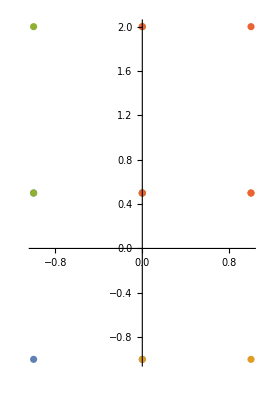

```mathematica
s=CreateRectangularMesh[{-1,-1},{1,2},1,1];
coords={{0,0},{1,0},{1,1},{0,1},{0.5,0.1},{1.1,0.5},{0.5,1.1},{0.1,0.5},{0.6,0.6}};
order=1;
nels=Length[s];
p=order;
matnode=Table[0,{nels}];
For[i=1,i≤nels,i++,
matnode[[i]]=nodes[p,s[[i]]];
{ek,ef}=CalcStiff[order,matnode[[i]]];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
];
ListPlot[matnode,AspectRatio->Automatic]
```

```mathematica
Assemble[order_,mesh_]:=Block[{nodevec,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,nels,ss},
nels=Length[mesh];
Print[nels];
nodevec=ComputeNodeVec[nodes[order,mesh]];
sz=Length[nodevec];
(*sz=nels*order+1;*)
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;
For[k=1,k≤nels,k++,
ss=nodes[order,mesh[[k]]];
{Ke,Fe}=CalcStiff[order,ss];
rows=Length[Ke];
cols=rows;
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];

(* Dirichlet Boundary Conditions *)
(*For[  i=1,i≤sz,i++,
	Kglob[[1,i]]=0;
	Kglob[[sz,i]]=0;
	Kglob[[i,1]]=0;
	Kglob[[i,sz]]=0;
    ];
Kglob[[1,1]]=1;Kglob[[sz,sz]]=1;
Fglob[[1]]=0;Fglob[[sz]]=0;*)

{Kglob,Fglob}
]
```

```mathematica
Assemble[order_,mesh_]:=Block[{nodevec,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,nels,ss},
nels=Length[mesh];
Print[nels];
nodevec=ComputeNodeVec[nodes[order,mesh]];
sz=Length[nodevec];
(*sz=nels*order+1;*)
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;
For[k=1,k≤nels,k++,
ss=nodes[order,mesh[[k]]];
{Ke,Fe}=CalcStiff[order,ss];
rows=Length[Ke];
cols=rows;
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];

(* Dirichlet Boundary Conditions *)
(*For[  i=1,i≤sz,i++,
	Kglob[[1,i]]=0;
	Kglob[[sz,i]]=0;
	Kglob[[i,1]]=0;
	Kglob[[i,sz]]=0;
    ];
Kglob[[1,1]]=1;Kglob[[sz,sz]]=1;
Fglob[[1]]=0;Fglob[[sz]]=0;*)

{Kglob,Fglob}
]
```

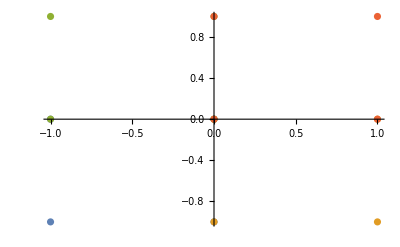

4

xi = -0.57735

eta = 0.57735

ek =(-0.163675 | 0.0193376 | 0.216506 | -0.0721688
0.0193376 | -0.0193376 | -0.0721688 | 0.0721688
0.216506 | -0.0721688 | -0.413675 | 0.269338
-0.0721688 | 0.0721688 | 0.269338 | -0.269338)

xi = 0.57735

eta = 0.57735

ek =(-0.0193376 | 0.0193376 | 0.0721688 | -0.0721688
0.0193376 | -0.163675 | -0.0721688 | 0.216506
0.0721688 | -0.0721688 | -0.269338 | 0.269338
-0.0721688 | 0.216506 | 0.269338 | -0.413675)

xi = -0.57735

eta = -0.57735

ek =(0.269338 | -0.269338 | -0.0721688 | 0.0721688
-0.269338 | 0.413675 | 0.0721688 | -0.216506
-0.0721688 | 0.0721688 | 0.0193376 | -0.0193376
0.0721688 | -0.216506 | -0.0193376 | 0.163675)

xi = 0.57735

eta = -0.57735

ek =(0.413675 | -0.269338 | -0.216506 | 0.0721688
-0.269338 | 0.269338 | 0.0721688 | -0.0721688
-0.216506 | 0.0721688 | 0.163675 | -0.0193376
0.0721688 | -0.0721688 | -0.0193376 | 0.0193376)

xi = -0.57735

eta = 0.57735

ek =(-0.163675 | 0.0193376 | 0.216506 | -0.0721688
0.0193376 | -0.0193376 | -0.0721688 | 0.0721688
0.216506 | -0.0721688 | -0.413675 | 0.269338
-0.0721688 | 0.0721688 | 0.269338 | -0.269338)

xi = 0.57735

eta = 0.57735

ek =(-0.0193376 | 0.0193376 | 0.0721688 | -0.0721688
0.0193376 | -0.163675 | -0.0721688 | 0.216506
0.0721688 | -0.0721688 | -0.269338 | 0.269338
-0.0721688 | 0.216506 | 0.269338 | -0.413675)

xi = -0.57735

eta = -0.57735

ek =(0.269338 | -0.269338 | -0.0721688 | 0.0721688
-0.269338 | 0.413675 | 0.0721688 | -0.216506
-0.0721688 | 0.0721688 | 0.0193376 | -0.0193376
0.0721688 | -0.216506 | -0.0193376 | 0.163675)

xi = 0.57735

eta = -0.57735

ek =(0.413675 | -0.269338 | -0.216506 | 0.0721688
-0.269338 | 0.269338 | 0.0721688 | -0.0721688
-0.216506 | 0.0721688 | 0.163675 | -0.0193376
0.0721688 | -0.0721688 | -0.0193376 | 0.0193376)

xi = -0.57735

eta = 0.57735

ek =(-0.163675 | 0.0193376 | 0.216506 | -0.0721688
0.0193376 | -0.0193376 | -0.0721688 | 0.0721688
0.216506 | -0.0721688 | -0.413675 | 0.269338
-0.0721688 | 0.0721688 | 0.269338 | -0.269338)

xi = 0.57735

eta = 0.57735

ek =(-0.0193376 | 0.0193376 | 0.0721688 | -0.0721688
0.0193376 | -0.163675 | -0.0721688 | 0.216506
0.0721688 | -0.0721688 | -0.269338 | 0.269338
-0.0721688 | 0.216506 | 0.269338 | -0.413675)

xi = -0.57735

eta = -0.57735

ek =(0.269338 | -0.269338 | -0.0721688 | 0.0721688
-0.269338 | 0.413675 | 0.0721688 | -0.216506
-0.0721688 | 0.0721688 | 0.0193376 | -0.0193376
0.0721688 | -0.216506 | -0.0193376 | 0.163675)

xi = 0.57735

eta = -0.57735

ek =(0.413675 | -0.269338 | -0.216506 | 0.0721688
-0.269338 | 0.269338 | 0.0721688 | -0.0721688
-0.216506 | 0.0721688 | 0.163675 | -0.0193376
0.0721688 | -0.0721688 | -0.0193376 | 0.0193376)

xi = -0.57735

eta = 0.57735

ek =(-0.163675 | 0.0193376 | 0.216506 | -0.0721688
0.0193376 | -0.0193376 | -0.0721688 | 0.0721688
0.216506 | -0.0721688 | -0.413675 | 0.269338
-0.0721688 | 0.0721688 | 0.269338 | -0.269338)

xi = 0.57735

eta = 0.57735

ek =(-0.0193376 | 0.0193376 | 0.0721688 | -0.0721688
0.0193376 | -0.163675 | -0.0721688 | 0.216506
0.0721688 | -0.0721688 | -0.269338 | 0.269338
-0.0721688 | 0.216506 | 0.269338 | -0.413675)

xi = -0.57735

eta = -0.57735

ek =(0.269338 | -0.269338 | -0.0721688 | 0.0721688
-0.269338 | 0.413675 | 0.0721688 | -0.216506
-0.0721688 | 0.0721688 | 0.0193376 | -0.0193376
0.0721688 | -0.216506 | -0.0193376 | 0.163675)

xi = 0.57735

eta = -0.57735

ek =(0.413675 | -0.269338 | -0.216506 | 0.0721688
-0.269338 | 0.269338 | 0.0721688 | -0.0721688
-0.216506 | 0.0721688 | 0.163675 | -0.0193376
0.0721688 | -0.0721688 | -0.0193376 | 0.0193376)

(0.5 | -0.5 | 0. | 0. | 0 | 0 | 0 | 0 | 0
-0.5 | 1. | -0.5 | -1.38778×10^-17 | 0. | 0 | 0 | 0 | 0
0. | -0.5 | 0.5 | 0. | -1.38778×10^-17 | 0. | 0 | 0 | 0
0. | -1.38778×10^-17 | 0. | -2.22045×10^-16 | 0. | -1.38778×10^-17 | 0. | 0 | 0
0 | 0. | -1.38778×10^-17 | 0. | -0.5 | 0.5 | -1.38778×10^-17 | 0 | 0
0 | 0 | 0. | -1.38778×10^-17 | 0.5 | -1. | 0.5 | 0 | 0
0 | 0 | 0 | 0. | -1.38778×10^-17 | 0.5 | -0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0.189815
0.324074
0.189815
0.
-0.189815
-0.324074
-0.189815
0
0)

```mathematica
s=CreateRectangularMesh[{-1,-1},{1,1},1,1];
ListPlot[s]
p=1;
{Kglob,Fglob}=Assemble[p,s];
Kglob//MatrixForm
Fglob//MatrixForm
```